```mathematica
Dd (*length of side*)
τ[i_]:= 10^i 10 Dd (*the adversary pours τ units of water each iteration.  i is the *

time interval*)
{10 L τ[i], (10 L + el)τ[i]}
```

Dd

{10^(2+i) Dd L,10^(1+i) Dd (el+10 L)}

```mathematica
25^2
```

625

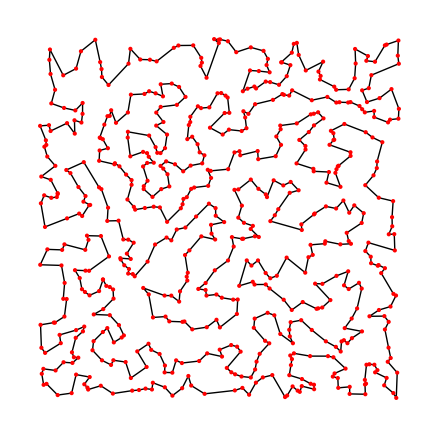

```mathematica
p=RandomReal[10,{25^2,2}];
tour = FindShortestTour[p];
Graphics[{Line[p⟦Last[tour]⟧],PointSize[Medium],Red,Point[p]}]
```

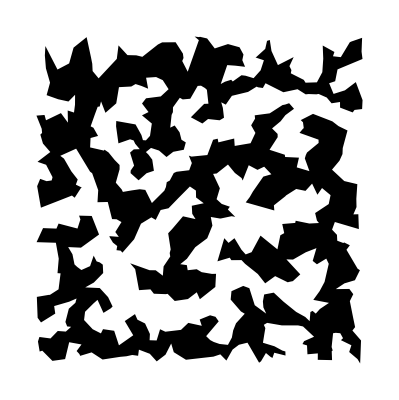

```mathematica
Graphics[Polygon[p⟦Last[tour]⟧]]
```